# NG_4 T_01 ШпакАндрей. Многослойный персептрон

Искусственная нейросеть и логические операции. Реализуйте три разных нейросети небольшого размера, архитектуры которых приведены на Рис.1. В качестве функции активации используйте пороговую функцию UnitSteppaclet:ref/UnitStep. Математическая модель нейрона (нейросети kmANN21) описывается формулой (DisplayFormulaNumbered).

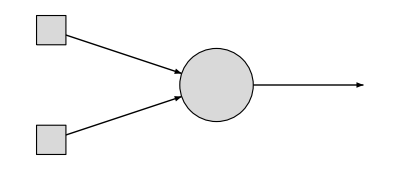
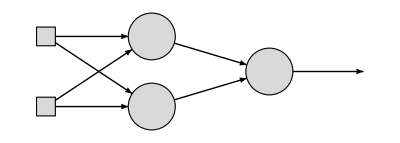
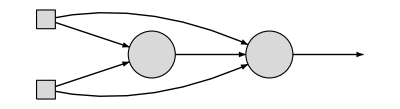
-Graphics-kmANN21 | -Graphics-kmANN221 | -Graphics-kmANN211
Рис 1. Искусственные нейросети

kmANN21_(W⃗)(x⃗):=UnitStep(w_1 x_1+w_2 x_2+w_0)

Решение:

```mathematica
ClearAll[kmANN21,kmANN221,kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN221[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{W11.{x1,x2,1},W12.{x1,x2,1},1}];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=W2.{x1,W1.{x1,x2,1},x2,1}
```

Используя построенные нейросети, реализуем три логических операции: Andpaclet:ref/And, Orpaclet:ref/Or, Xorpaclet:ref/Xor. Для этого подготовим таблицу всевозможных пар логических констант.

```mathematica
BooleDS=Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Do[Print[op,":",Table[StringJoin[ToString[BooleDS[[i]]]," → ",ToString[Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]]],{i,Length[BooleDS]}]],{op,{And,Or,Xor}}]
```

And:{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

Or:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 1}

Xor:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 0}

# Как я разбирался с заданиями

1.

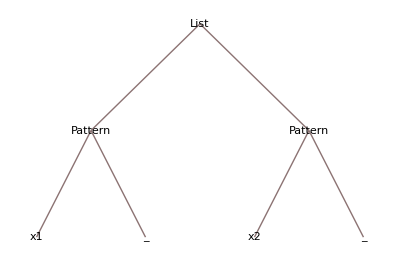

```mathematica
(*Вспоминаю про шаблоны с помощью TreeForm*)
{x1_,x2_}//TreeForm
```

```mathematica
(*Что такое префикс и для чего он нужен при работе в первом задании. Но так и не понял. ВОПРОС*)
Prefix[f@{z1, z2}]
```

f@{z1,z2}

```mathematica
{1, 2, 3}*{4,5,6}
```

{4,10,18}

```mathematica
Plus@@({1, 2, 3}*{4,5,6})
```

32

```mathematica
(*Можно и использовать Dot, это более лаконично*)
{1, 2, 3}.{4,5,6}
```

32

```mathematica
(*Разбираюсь со второй функцией kmANN221*)
W11={w1,w2}
x1*W11
```

{w1,w2}

{w1 x1,w2 x1}

```mathematica
x1.W11
```

x1.{w1,w2}

```mathematica
const=1
const.{w1,w2}
const.{1,2}
{const, const}.{w1,w2}
```

1

1.{w1,w2}

1.{1,2}

w1+w2

```mathematica
W12={w3,w4}
x1*W11
x2*W12
```

{w3,w4}

{w1 x1,w2 x1}

{w3 x2,w4 x2}

```mathematica
x1*W11[[1]]
x2*W12[[1]]
```

w1 x1

w3 x2

```mathematica
x1*W11[[2]]
x2*W12[[2]]
```

w2 x1

w4 x2

```mathematica
(x1*W11[[1]]).(x2*W12[[1]])
```

(w1 x1).(w3 x2)

```mathematica
(x1*W11[[2]]).(x2*W12[[2]])
```

(w2 x1).(w4 x2)

```mathematica
W2.{(x1*W11[[1]]).(x2*W12[[1]]),(x1*W11[[2]]).(x2*W12[[2]])}
```

Dot::dotsh: Tensors {w3,w4,w5,w0} and {(w1 x1).(w3 x2),(w2 x1).(w4 x2)} have incompatible shapes.

{w3,w4,w5,w0}.{(w1 x1).(w3 x2),(w2 x1).(w4 x2)}

```mathematica
(*Как мне казалось, я сделал правильно, но, пересматривая условие я понял, что сделал не так: забыл про w0 и перепутал весь принцип формирования линейной комбинации значений с весами. Поэтому заново и более внимательно и пошагово ещё раз.*)
```

-Graphics-

```mathematica
W11={w1,w2,w0};
W12={w3,w4,w0};
W11.{x1,x2,1}
W12.{x1,x2,1}
```

w0+w1 x1+w2 x2

w0+w3 x1+w4 x2

```mathematica
W2={w5,w6,w0};
W2.{W11.{x1,x2,1},W12.{x1,x2,1},1}
```

w0+w5 (w0+w1 x1+w2 x2)+w6 (w0+w3 x1+w4 x2)

```mathematica
(*Остается добавить только UnitStep*)
```

```mathematica
(*Разбираюсь с третьей функцией kmANN211, снова пошагово*)
-Graphics-
```

-Graphics-

```mathematica
W1={w1,w2,w0};
W2={w3,w4,w5,w0};
W1.{x1,x2,1}
```

w0+w1 x1+w2 x2

```mathematica
W2.{x1,W1.{x1,x2,1},x2,1}
```

w0+w3 x1+w5 x2+w4 (w0+w1 x1+w2 x2)

```mathematica
(*Теперь вспоминаю, как работает Table:*)
BooleDS=Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
(*Для начала:*)
Table[x,{x,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[{x,y},{x,0,2},{y,0,3}]
(*Получается, что это как список из итераций, где x отвечает за внешний цикл, а y за внутренний*)
```

{{{0,0},{0,1},{0,2},{0,3}},{{1,0},{1,1},{1,2},{1,3}},{{2,0},{2,1},{2,2},{2,3}}}

```mathematica
(*Теперь Do:*)
Do[Print[BooleDS],{op,{And,Or,Xor}}];
(*Dopaclet:ref/Do[expr,{i,{Subscript[i, 1],Subscript[i, 2],…}}]*)
```

{{0,0},{0,1},{1,0},{1,1}}

{{0,0},{0,1},{1,0},{1,1}}

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
(*Формирование таблицы из операций оказалось сложным после перерыва в использовании вольфрама. Я использовал следующие подходы:*)
```

```mathematica
(*Вспомнил, как работает Part*)
BooleDS[[1,1]]
```

0

```mathematica
(*And не работал для единиц и нулей, в отличие от своего алиаса*)
1^1
```

1

```mathematica
(*И я решил это так:*)
And[1==1,1==1]
```

True

```mathematica
(*Составная часть моего списка для каждой из операций можнет выглядеть, например, так (op заменил на And):*)
it=1;
{BooleDS[[it]],Text[" → "],Boole[And[BooleDS[[it,1]]==1,BooleDS[[it,2]]==1]]}
```

{{0,0}, → ,0}

```mathematica
(*Тогда самый простой вариант: Do работает три раза для каждой из операций, значит внутри должен быть еще какой-то цикл для каждого списочка в BooleDS. Но это не совсем то, что нужно.*)
Do[Table[Print[op,Text[": "],BooleDS[[i]]," → ",Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]],{i,Length[BooleDS]}],{op,{And,Or,Xor}}];
```

And: {0,0} → 0

And: {0,1} → 0

And: {1,0} → 0

And: {1,1} → 1

Or: {0,0} → 0

Or: {0,1} → 1

Or: {1,0} → 1

Or: {1,1} → 1

Xor: {0,0} → 0

Xor: {0,1} → 1

Xor: {1,0} → 1

Xor: {1,1} → 0

```mathematica
(*Точка с запятой разделяет команды им ожно сделать аккуратней, но это все ещё не как в условии:*)
Do[Print[op,Text[": "]];Table[Print[BooleDS[[i]]," → ",Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]],{i,Length[BooleDS]}],{op,{And,Or,Xor}}];
```

And:

{0,0} → 0

{0,1} → 0

{1,0} → 0

{1,1} → 1

Or:

{0,0} → 0

{0,1} → 1

{1,0} → 1

{1,1} → 1

Xor:

{0,0} → 0

{0,1} → 1

{1,0} → 1

{1,1} → 0

```mathematica
(*А тут все вообще исчезло:*)
Do[Print[op,Text[": "]];Table[{BooleDS[[i]]," → ",Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]},{i,Length[BooleDS]}],{op,{And,Or,Xor}}]
```

And:

Or:

Xor:

```mathematica
(*Тогда я решил попробовать: что будет, если я сформирую целую строку в Table с помощью функции StringJoin, которую будет выводить Print три раза в Do? Начал с малого, забравшись внуть Table и убрав оттуда Print (op заменил на And):*)
Table[{BooleDS[[i]]," → ",Boole[And[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]},{i,Length[BooleDS]}]
```

{{{0,0}, → ,0},{{0,1}, → ,0},{{1,0}, → ,0},{{1,1}, → ,1}}

```mathematica
(*Пробую использовать StringJoin для двух выражений:*)
Table[{StringJoin[ToString[BooleDS[[i]]]," → "],Boole[And[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]},{i,Length[BooleDS]}]
```

{{{0, 0} → ,0},{{0, 1} → ,0},{{1, 0} → ,0},{{1, 1} → ,1}}

```mathematica
(*Теперь для целого выражения:*)
Table[StringJoin[ToString[BooleDS[[i]]]," → ",ToString[Boole[And[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]]],{i,Length[BooleDS]}]
```

{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

```mathematica
(*Вот и итог:*)
Do[Print[op,":",Table[StringJoin[ToString[BooleDS[[i]]]," → ",ToString[Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]]],{i,Length[BooleDS]}]],{op,{And,Or,Xor}}]
```

And:{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

Or:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 1}

Xor:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 0}